## Here we calculate thermal - visco - elastic waves in water and below calculate how these waves reflect from a halfspace

```mathematica
ClearAll["Global`*"]
```

```mathematica
dir= NotebookDirectory[]
Needs["ThermalWaves`",dir<>"../packages/ThermalWaves.wl"];
Needs["ThermalPotentials`",dir<>"../packages/ThermalPotentials.wl"];
NotebookEvaluate[dir<>"../packages/ScatteringTW.nb"]
Names["ThermalWaves`*"]
?ThermalWaves
```

/home/art/drive-sheffield/Mathematica/LinearThermoViscoElasticity/examples/

{DisplacementTW,EnergyFluxTW,PlotTW,PlusTW,StressTW,ThermalWaves,TWQ,θTW}

```mathematica
(*Water: parameter values at θ0 = 25^o C*)
subN ={"μ"->1.3 10^-5,"κ"->0.58, "ημ"-> 8.9 10^-4, "ηβ"-> 2.47/3 10^-3,"ρ"-> 998,"Cv"-> 4.182 10^3,"T0"-> 298,"α"-> 2.57 10^-4,"β"-> 2.14 10^9,"L"-> 1};
subN ={"μ"->0.,"κ"->0.58, "ημ"-> 8.9 10^-4, "ηβ"-> 2.47/3 10^-3,"ρ"-> 998,"Cv"-> 4.182 10^3,"T0"-> 298,"α"-> 2.57 10^-4,"β"-> 2.14 10^9,"L"-> 1};

subN = AddToNsub@subN
```

{μ→0.,κ→0.58,ημ→0.00089,ηβ→0.000823333,ρ→998.,Cv→4182.,T0→298.,α→0.000257,β→2.14×10^9,L→1.,Cp→4224.21,cp2→2.16593×10^6,pT→1.63894×10^8,γ→1.01009,ηλ→0.00023,λ→2.14×10^9,LowFrequencyPressureWaveSpeed→1471.71}

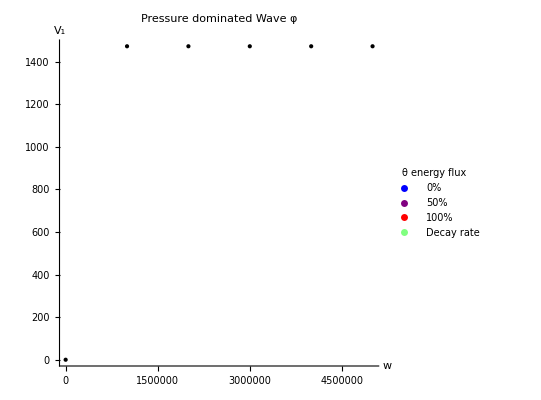

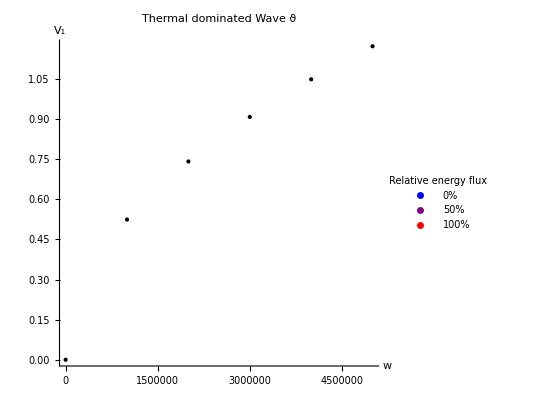

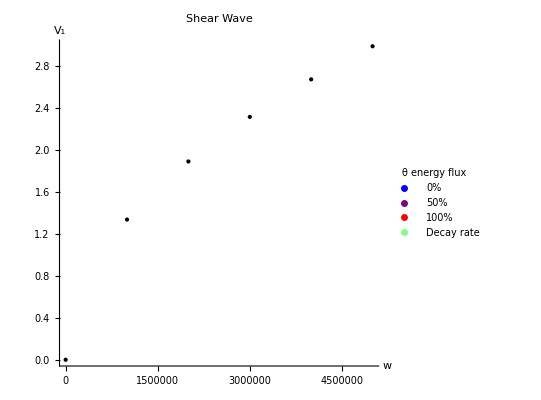

```mathematica
rngω= Range[1,10^5/2,10^4/4];
rngω= Range[5]10^6;
(*rngω ={1.,2.,3.};*)
(*rngω={1/10,10,10^3,10^5,10^8,10^10};*)

precision =15;
subN = SetPrecision[subN,precision];
rngω = SetPrecision[rngω,precision];

(*All waves will use the same wave number*)
{TWφ,TWϑ,Wψ}= ThermalWaves[subN,{1.,0.,0},rngω];
(*Explicit give wave numbers to all three waves*)
(*{TWφ,TWϑ,Wψ}= ThermalWaves[subN,{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}},rngω];*)

PlotTW[TWφ]
PlotTW[TWϑ,"ReferenceTW"->TWφ]
PlotTW[Wψ]
```

```mathematica
TWφ["WaveNumbers"]
TWϑ["WaveNumbers"]
Wψ["WaveNumbers"]
```

{{679.482+0.000316132 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{1358.96+0.00126453 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{2038.45+0.00284519 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{2717.93+0.00505811 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{3397.41+0.0079033 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{1.90638×10^6+1.90638×10^6 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{2.69602×10^6+2.69602×10^6 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{3.30194×10^6+3.30194×10^6 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{3.81275×10^6+3.81275×10^6 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{4.26279×10^6+4.26279×10^6 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

{{748782.+748782. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{1.05894×10^6+1.05894×10^6 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{1.29693×10^6+1.29693×10^6 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{1.49756×10^6+1.49756×10^6 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{1.67433×10^6+1.67433×10^6 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
(*Other functions *)

?StressTW
?DisplacementTW
?EnergyFluxTW
X= {0.,0., 0.}; 
vecK = {1.,1., 1.}; (*wave direction*)

u =  DisplacementTW[TWφ,X];
v = -ⅈ rngω u;
σ = StressTW[TWφ,X] ;
-1/2 Re@MapThread[Dot,{v*,σ}] (*Energy Flux, which is used to color the plots above*)
(*Short hand*)
EnergyFluxTW[TWφ] ;
```

{{-9.15018×10^11,0.,0.},{-9.15166×10^11,0.,0.},{-9.15193×10^11,0.,0.},{-9.15202×10^11,0.,0.},{-9.15207×10^11,0.,0.}}

### Wave reflection and transmission

```mathematica
(* Below we use the function ScatteredTW, here is how it works:
{TWRs,TWTs}= ScatteredTW[TWin,TWs,TW2s,opts]; 
 where TWin is the incident wave, ex: TWin = TWφ, the wavenumbers given by TWin["WaveNumbers"] determine the direction of the incident wave, TWin["WaveNumbers"][[1]] is the p-wavenumber vector and TWin["WaveNumbers"][[2]] is the shear-wavenumber vector;TWs is a list with of the form TWs = {TWφ,TWϑ,Wψ} where each of there have the wavenumber and wavevectors of the top material (where the incident wave travels);
TW2s is a list with of the form TW2s = {TW2φ,TW2ϑ,W2ψ} where each of these have the wavenumber and wavevectors of the bottom material where waves are transmitted;
 TWRs and TWTs are similar lists, but now have the correct wavenumber and wavevectors to satisfy scattering from the surface z=0.   
*)

(*parameters for the incident medium*)
subN ={"μ"->1.3 10^-5,"κ"->0.58, "ημ"-> 8.9 10^-4, "ηβ"-> 2.47/3 10^-3,"ρ"-> 998,"Cv"-> 4.182 10^3,"T0"-> 298,"α"-> 2.57 10^-4,"β"-> 2.14 10^9,"L"-> 1};
 subN=AddToNsub@subN;
(*parameters for the transmitting medium*)
subNT ={"μ"->4.3 10^-5,"κ"->1.08, "ημ"-> 8.9 10^-5, "ηβ"-> 2.47/3 10^-4,"ρ"-> 698,"Cv"-> 10.182 10^3,"T0"-> 298,"α"-> 6.57 10^-4,"β"-> 2.14 10^10,"L"-> 1};
subNT =AddToNsub@subNT;
```

{height→0,ClampedBC→False,FreeBC→False,FixedTempBC→False,NoHeatFluxBC→False}

NSolve::precw: The precision of the argument function ({(0.+0. ⅈ)-(480.466+0.000223539 ⅈ) Ψ2[T]-(1.98024×10^6+1.98024×10^6 ⅈ) Ψ3[T],(0.+0. ⅈ)+ⅈ («1»)-ⅈ ((1.98024×10^6+1.98024×10^6 ⅈ) Ψ2[T]-(480.466+«23» ⅈ) Ψ3[T]),«1»,(0.+0. ⅈ)-(480.466+0.000223539 ⅈ) Ψ2[R]+(748782.+748782. ⅈ) Ψ3[R]}) is less than WorkingPrecision (19.).

NSolve::precw: The precision of the argument function ({0.57999999999999996003 ((0.00063979-480.466 ⅈ)+(1.90638×10^6+1.90638×10^6 ⅈ) ζ0[R]-(0.00063979-480.466 ⅈ) ξ0[R])-1.0800000000000000711 ((-2.13652×10^6-2.13652×10^6 ⅈ) ζ0[T]+(455.343+«23» ⅈ) ξ0[T]),«1»,«1»,«1»,«1»,«1»}) is less than WorkingPrecision (19.).

NSolve::precw: The precision of the argument function ({(0.+0. ⅈ)-(960.933+0.000894156 ⅈ) Ψ2[T]-(2.80048×10^6+2.80048×10^6 ⅈ) Ψ3[T],(0.+0. ⅈ)+ⅈ («1»-«1»)-ⅈ ((2.80048×10^6+2.80048×10^6 ⅈ) Ψ2[T]-(960.933+«21» ⅈ) Ψ3[T]),«1»,(0.+0. ⅈ)-(960.933+0.000894156 ⅈ) Ψ2[R]+(1.05894×10^6+1.05894×10^6 ⅈ) Ψ3[R]}) is less than WorkingPrecision (19.).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

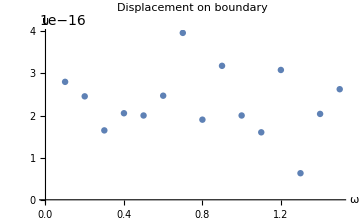
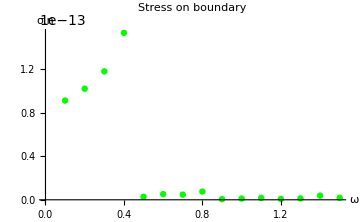
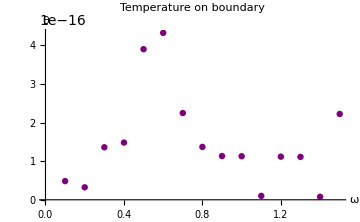
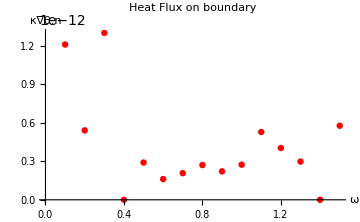

```mathematica
rngω = Range[1,15] 10^6;
(*rngω = {9.7 10^7};*)
rngθ = Range[0.,π/4,π/10];
(*Calculating the wavenumbers needs high precision*)
precision =20;
subN = Quiet@SetPrecision[subN,precision];
subNT =Quiet@ SetPrecision[subNT,precision];
rngω = Quiet@SetPrecision[rngω,precision];

(*All waves will use the same wave number*)
TWs= ThermalWaves[subN,{0,-1,-1},rngω];
TW2s= ThermalWaves[subNT,{0,0,-1},rngω];

(*A global options set*)
opts = {"height"->0,"FreeBC"->False,"ClampedBC"->False, "NoHeatFluxBC"->False,"FixedTempBC"->False};
Options@ScatteredTW
TWin = TWs[[1]] ;(*Choose an incident wave*)
{TWRs,TWTs}= ScatteredTW[TWin,TWs,TW2s,opts];

(*Check Boundary condtions divided by the incident wave*)
Show[#,ImageSize->Medium]&/@PlotBCTW[TWin,TWRs,TWTs,opts]
```

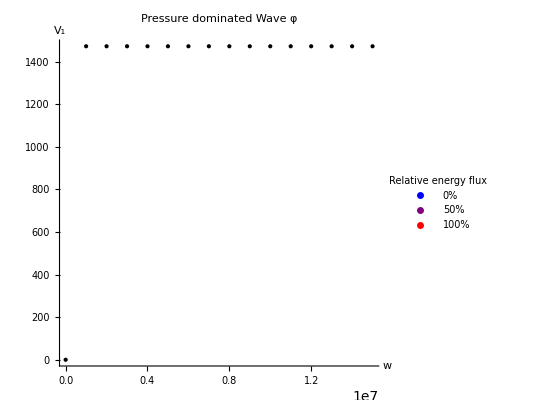
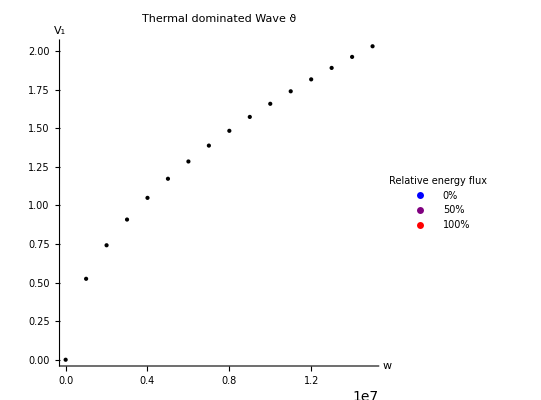
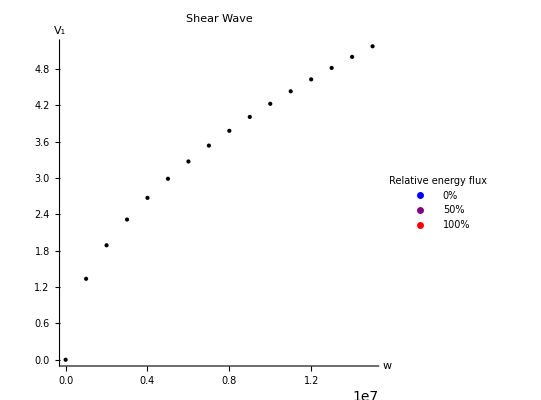

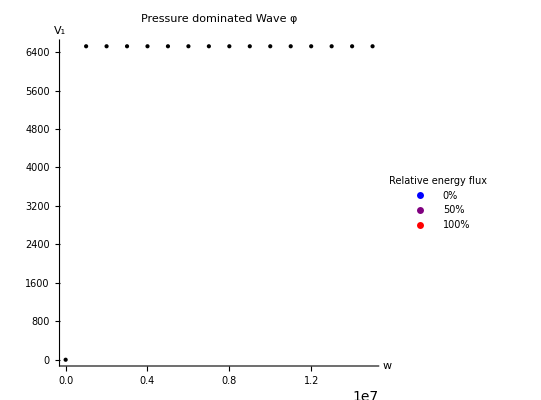
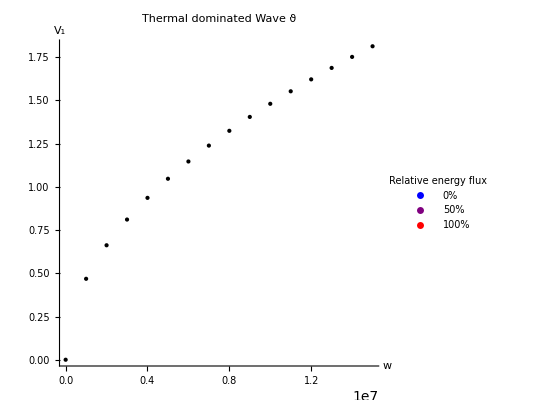
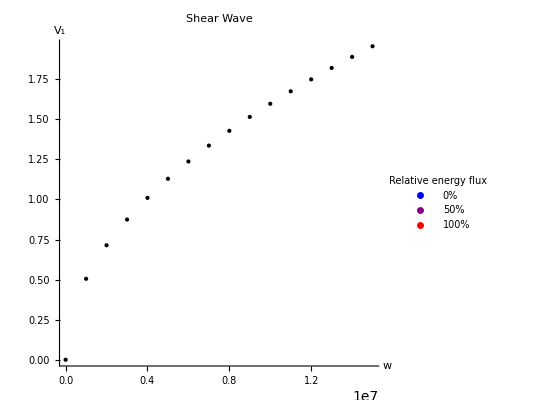

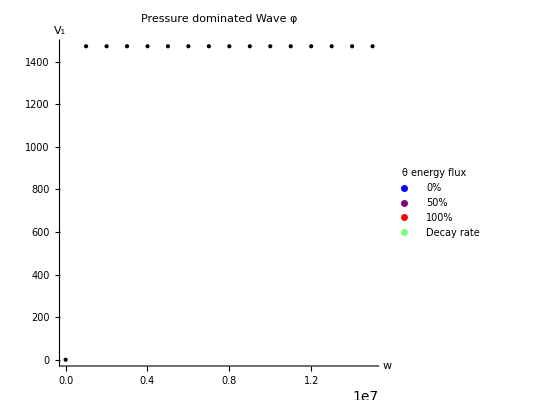
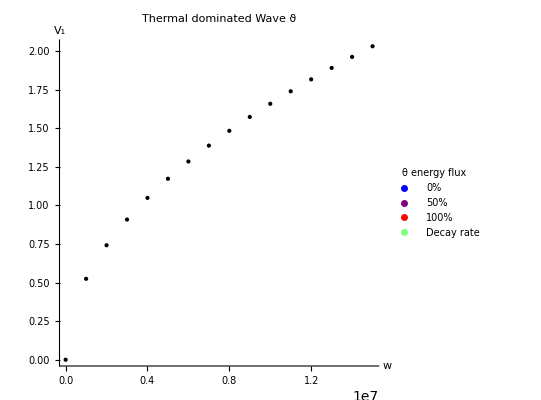

```mathematica
PlotTW[#,"ReferenceTW"->TWin]&/@TWRs
PlotTW[#,"ReferenceTW"->TWin]&/@TWTs
PlotTW[#]&/@TWRs
PlotTW[#]&/@TWTs
```

```mathematica
(*An energy flux check*)

(*Energy flux in upper halfspace*)
X = {0,0,"height"/.opts};
us=DisplacementTW[TWin,X] +Plus@@(DisplacementTW[#,X]&/@TWRs);
vs = -I TWin["rngω"] us;
σs=StressTW[TWin,X] +Plus@@(StressTW[#,X]&/@TWRs);
EIR= -0.5Re@MapThread[Dot,{vs*,σs}];

(*Energy flux in lower halfspace*)
X = {0,0,"height"/.opts};
us=Plus@@(DisplacementTW[#,X]&/@TWTs);
vs = -I TWTs[[1]]["rngω"] us;
σs=Plus@@(StressTW[#,X]&/@TWTs);
ET=-0.5Re@MapThread[Dot,{vs*,σs}];

(*total Energy going down + total Energy going up  *)
EIR.{0,0,1} +ET.{0,0,-1} (*should be approximately zero*)
```

{-0.000411987,-0.000976563,0.0021286,-0.000572205,-0.00123978,-0.00105667,-0.000106812,-0.000167847,-0.000221252,0.000724792,-0.000656128,-0.000518799,0.000305176,0.00112152,0.000114441}